/home/steven/Nextcloud/NetDisk/Works/24.08.19 NonBoltz/Code/CodeSum/supp

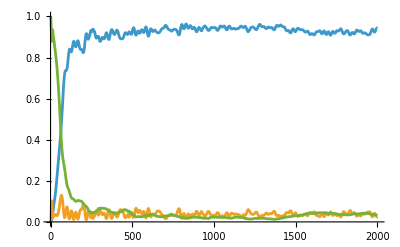

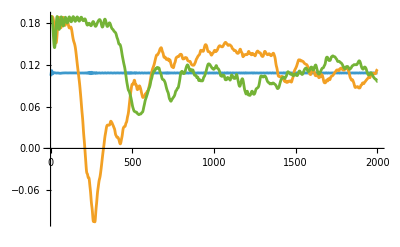

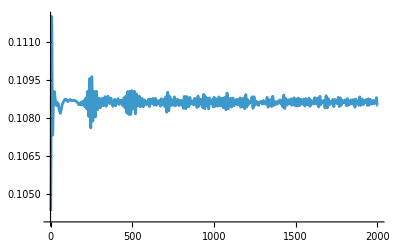

-Graphics-

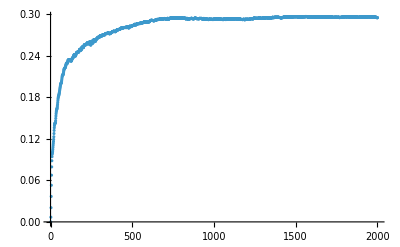

-Graphics-

snt.csv

pnt.csv

Et.csv

```mathematica
SetDirectory[NotebookDirectory[]]
Tnum=2000;
Tmax=500;
J=0.13;Ω=-1;ω=-1.19;
E0=0.; Ep1=Ω+ω; Em1=Ω-ω;

Pnat=Import["N30long.wdx"];
a=2;NN=30;
Tnum=Length[Pnat⟦1,1,;;⟧];
EntroS[P_]:=Sum[
If[0<P⟦n⟧<1,-P⟦n⟧Log[P⟦n⟧],0],{n,1,Length[P]}];
Snt=ParallelTable[EntroS[Pnat⟦n,;;,t⟧],
{n,1,NN},{t,1,Tnum}]; (* Entropy Subscript[S, n](t) *)
St=1/NN Table[Total[Snt⟦;;,t⟧],{t,1,Tnum}];
(*DDt=1/NN Table[Total[Pnat⟦;;,1,t⟧+Pnat⟦;;,3,t⟧],{t,1,Tnum}];*)
Pat=1./NN Table[Total[Pnat⟦;;,a,t⟧],{a,1,3},{t,1,Tnum}];

Et=Em1*Pat⟦1,;;⟧+E0*Pat⟦2,;;⟧+Ep1*Pat⟦3,;;⟧;
Et1=Em1*Pnat⟦5,1,;;⟧+E0*Pnat⟦5,2,;;⟧+Ep1*Pnat⟦5,3,;;⟧;
Et2=Em1*Pnat⟦10,1,;;⟧+E0*Pnat⟦10,2,;;⟧+Ep1*Pnat⟦10,3,;;⟧;


Snt=RotateLeft[Snt,20];
pt=RotateLeft[Pnat⟦;;,2,;;⟧,20];

ListPlot[{Pnat⟦1,1,;;⟧,Pnat⟦1,2,;;⟧,Pnat⟦1,3,;;⟧},PlotRange->All,Joined->True]
ListPlot[{Et,Et1,Et2},PlotRange->All,Joined->True]
ListPlot[Et,PlotRange->All,Joined->True]
ListDensityPlot[Snt,PlotRange->All,InterpolationOrder->0]
ListPlot[St,PlotRange->All]
ListDensityPlot[pt,PlotRange->All,InterpolationOrder->0]

Export["snt.csv",Snt,"CSV"]
Export["pnt.csv",pt,"CSV"]
Export["Et.csv",{Et,Et1,Et2},"CSV"]
```

```mathematica
ftSnt=Fourier[Snt];
ftSnt=RotateRight[ftSnt,{14,1000}];
ftSnt=Transpose[ftSnt];
ListDensityPlot[Abs[ftSnt],PlotRange->{All,{900,1100},{0,2}},InterpolationOrder->0]
```

-Graphics-

```mathematica
Mean[Et⟦1000;;⟧]
Mean[Pat⟦1,1500;;⟧]
Mean[Pnat⟦5,1,1500;;⟧]
```

0.108627

0.931184

0.930066

```mathematica
Dimensions[ftSnt]
```

{2001,30}

```mathematica
Export["ftSnt-long-112.csv",Abs[ftSnt],"CSV"]
```

ftSnt-long-112.csv